```mathematica
ClearAll["Global`*"]
```

```mathematica
i=3; (*number of days to simulate*)

imax=6; μ=48; d=0.00025;c=0.00025;(*sets parameters*) (*from 2008 paper*)
(*d = death rate of RBCs - what about bystander killing? Cromer et al. est. is 0.0095 for first six days of infection*)

βRA=0.000274 ; βRB=0.000274(*0.00015*); (*invasion rates - normo rate from 2008 paper*)
βNA=0.00000183; βNB=0.00000183;
ωR=9;ωE=9;(*Burst sizes for reticulocytes and normocytes, from July 2017 paper *)

θ=0.1; θan=0.52509; (*recovery coefficient for erythropoesis, from 2008 paper*)

τ=2; (*lag time for erythropoesis, from 2008 paper*)
κ=6000000; (*steady state RBC density, from Cromer paper*)
```

```mathematica
(*Initial conditions at time of transfusion*)
PAnext=387628;
PBnext=91420;
R1next=60000;
R2next=60000;
R3next=60000;
Ernext=5820000;
IA1next=0;
IA2next=0;
IA3next=0;
IB1next=0;
IB2next=0;
IB3next=0;
InfNAnext=0;
InfNBnext=0;

(*Creates empty lists*)
PAlist={};
PBlist={};
Rlist={};
Erlist={};
```

```mathematica
Do[{
sys={
PA'[t]== -PA[t](βRA*(R1[t]+IA1[t]+IB1[t]+R2[t]+IA2[t]+IB2[t]+R3[t]+IA3[t]+IB3[t])+βNA*(Er[t]+InfNA[t]+InfNA[t]))-μ*PA[t],
PB'[t]== -PB[t]*(βRB*(R1[t]+IA1[t]+IB1[t]+R2[t]+IA2[t]+IB2[t]+R3[t]+IA3[t]+IB3[t])+βNB*(Er[t]+InfNA[t]+InfNB[t]))-μ*PB[t],
R1'[t]==-βRA*PA[t]*R1[t]-βRB*PB[t]*R1[t],
R2'[t]==-βRA*PA[t]*R2[t]-βRB*PB[t]*R2[t],
R3'[t]==-βRA*PA[t]*R3[t]-βRB*PB[t]*R3[t],
Er'[t]==-βNA*PA[t]*Er[t]-βNB*PB[t]*Er[t],
IA1'[t]== βRA*PA[t]*R1[t],
IA2'[t]== βRA*PA[t]*R2[t],
IA3'[t]== βRA*PA[t]*R3[t],
IB1'[t]== βRB*PB[t]*R1[t],
IB2'[t]== βRB*PB[t]*R2[t],
IB3'[t]== βRB*PB[t]*R3[t],
InfNA'[t]== βNA*PA[t]*Er[t],
InfNB'[t]==βNB*PB[t]*Er[t],
PA[0]==PAnext,
PB[0]==PBnext,
R1[0]==R1next,
R2[0]==R2next,
R3[0]==R3next,
Er[0]==Ernext,
IA1[0]==IA1next,
IA2[0]==IA2next,
IA3[0]==IA3next,
IB1[0]==IB1next,
IB2[0]==IB2next,
IB3[0]==IB3next,
InfNA[0]==InfNAnext,
InfNB[0]==InfNBnext};

(*Solve system of equations*)
sol=NDSolve[sys, {PA,PB,R1,R2, R3, Er, IA1,IA2,IA3,IB1,IB2,IB3, InfNA, InfNB},{t,0,100}];
(*Store output for t = 0, 0.01 and 0.5*);

AppendTo[PAlist,{PA[0]/.sol,PA[0.01]/.sol,PA[0.5]/.sol}];
AppendTo[PBlist,{PB[0]/.sol,PB[0.01]/.sol,PB[0.5]/.sol}];
AppendTo[Rlist,{(R1[0]/.sol)+(R2[0]/.sol)+(R3[0]/.sol),(R1[0.01]/.sol)+(R2[0.01]/.sol)+(R3[0.01]/.sol),(R1[0.5]/.sol)+(R2[0.5]/.sol)+(R3[0.5]/.sol)}];
AppendTo[Erlist,{Er[0]/.sol,Er[0.01]/.sol,Er[0.5]/.sol}];

Clear[PAnext, PBnext,R1next,R2next,R3next,Ernext,IA1next,IA2next,IA2next,IA3next,IB1next,IB2next,IB3next, InfNAnext,InfNBnext];

(*Set next-day starting values*)
PAnext=First[First[(βRA*{(IA1[100]/.sol)+(IA2[100]/.sol)+(IA3[100]/.sol)}+βNA*(InfNA[100]/.sol))*(1-c)]];(*should be 0*)
PBnext=First[First[(βRB*{(IB1[100]/.sol)+(IB2[100]/.sol)+(IB3[100]/.sol)}+βNB*(InfNB[100]/.sol))*(1-c)]];
R1next=First[0.5*(κ-(Er[0]/.sol)-(R1[0]/.sol)-(R2[0]/.sol)-(R3[0]/.sol))];
R2next=First[(R1[100]/.sol)*(1-d)];
R3next=First[(R2[100]/.sol)*(1-d)];
Ernext=First[((Er[100]/.sol)+(R3[100]/.sol))*(1-d)];
IA1next=0;(*okay to not age because they burst anyway?*)
IA2next=0;
IA3next=0;
IB1next=0;
IB2next=0;
IB3next=0;
InfNAnext=0;
InfNBnext=0;

Clear[sys];}, {i}];
```

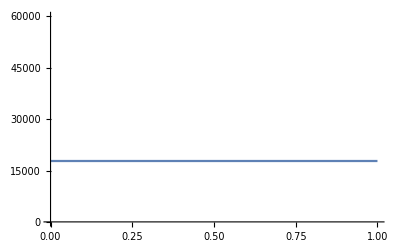

```mathematica
Plot[R3[t]/.sol,{t,0,1}, PlotRange->{0,60000}]
```

```mathematica
First[(βRA*{(IA1[100]/.sol)+(IA2[100]/.sol)+(IA3[100]/.sol)}+βNA*(InfNA[100]/.sol))*(1-c)]
```

{305.436}

```mathematica
R3[100]/.sol
```

{3.11312×10^-12}

```mathematica
PAlist
```

{{{387628.},{131648.},{4.56412×10^-10}},{{28.134},{14.2043},{-6.57781×10^-11}},{{0.00110725},{0.000461627},{2.31633×10^-10}}}

```mathematica
Rlist
```

{{{180000.},{80661.8},{53383.7}},{{35580.3},{35577.8},{35575.3}},{{105347.},{105347.},{105347.}}}

```mathematica
Erlist
```

{{{5.82×10^6},{5.78888×10^6},{5.77295×10^6}},{{5.78929×10^6},{5.78929×10^6},{5.78929×10^6}},{{5.80562×10^6},{5.80562×10^6},{5.80562×10^6}}}

```mathematica
PBlist
```

{{{91420.},{31055.},{1.0933×10^-10}},{{6.6363},{3.35054},{-1.55159×10^-11}},{{0.000261181},{0.00010889},{5.4638×10^-11}}}